```mathematica
Clear["Global`*"];
```

Model is two RC elements in series.  The first, with resistance 9R and variable capacitance C represents the oscilloscope 10x passive probe.  The second, with resistance R= 1 MΩ and capacitance C_0, represents the scope input and the combined effects of scope input and cable impedances. 

Here, we scale time so that RC_0=1 and τ is in units of 9RC.  τ=1 then matches the impedance (the zero in the transfer function matches the pole), and the response is unity.  (We have multiplied by 10 to compensate for the 1:10 voltage reduction produced by the scope probe.

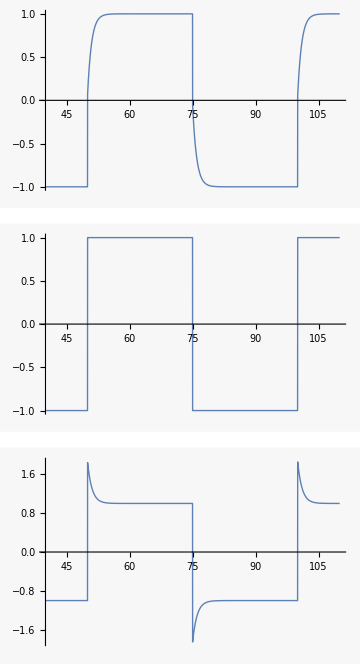

```mathematica
sys=TransferFunctionModel[(1+s τ)/(1+1/10 s(τ+9)),s];tmin=40;tmax=110;
sq[t_]:=Sign[Sin[2π t]]  (* SquareWave[t] has a bug :(  *)
y1=OutputResponse[sys/.τ->0.5,sq[t/50],{t,0,tmax}]//First;         
	     (* Mathematica has a bug if integration starts at t>0 *)
y2=OutputResponse[sys/.τ->1,sq[t/50],{t,0,tmax}]//First;
y3=OutputResponse[sys/.τ->1.5,sq[t/50],{t,0,tmax}]//First;

p1=Plot[y1,{t,tmin,tmax}];
p2=Plot[y2,{t,tmin,tmax},Exclusions->None];
p3=Plot[y3,{t,tmin,tmax}];
GraphicsColumn[{p1,p2,p3},ImageSize->Medium]
```

Export data

```mathematica
dt=0.1;
dat=Table[{y1,y2,y3},{t,0,tmax,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["oscilloscope.dat",dat];
*)
```